```mathematica
SetDirectory[NotebookDirectory[]];
<<"rotationtools.wl"
<<"kinematic_utils.m"
<<"MaTeX`"
```

```mathematica
T[x_]:=Transpose[x];
mf[x_]:=MatrixForm[x];
dim[x_]:=Dimensions[x];
```

```mathematica
(*Assuming all the legs are made of steel*)
```

```mathematica
(*Similar set of data for 6-RSS has shown that these values are too high*)
```

```mathematica
leglparam = {ro->0.04/2, ri->0.035/2, ρ-> 7858, lb->0.5, la->1.5};
legmparam = {ma->ρ*π*ri^2*la, mb-> ρ*π*(ro^2-ri^2)*lb, g->9.8}/.leglparam;
ibzi =  mb*(ri^2+ro^2)/2;
ibxi = mb*(3*(ro^2+ri^2)+lb^2)/12;
ibyi = mb*(3*(ro^2+ri^2)+lb^2)/12;

iazi =  ma*ri^2/2;
iaxi = ma*(3*ri^2+la^2)/12;
iayi = ma*(3*ri^2+la^2)/12;

(*Mass and inertial values are from the CAD model*)
datap ={rb->1, rt->0.5803, γt->0.6573, γb->0.2985};
tplparam = {ρ->2810, t->0.01}/.datap;
(*tpmparam = mtp-> ρ*t*3*√3/2*rt^2/.tplparam/.datap;*)
tpmparam = mtp-> 0.20339;
(*itpz = mtp*rt^2*(1-(2/3)*Sin[π/6]^2);
itpx = itpz/2;
itpy = itpz/2;*)
itpz = 2.343101;
itpx = 1.17172;
itpy =  1.17172;

(*Assuming manipulator is symmetric in construction*)
Ibi = {{ibxi, 0, 0}, {0,ibyi, 0}, {0, 0,ibzi}};
Iai ={{iaxi,0,0}, {0,iayi,0},{0,0,iazi}};
Itp = {{itpx, 0, 0}, {0, itpy, 0}, {0, 0, itpz}};
```

```mathematica
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;
```

```mathematica
b = Table[Symbol["b"<>ToString[i]],{i, 6}];
```

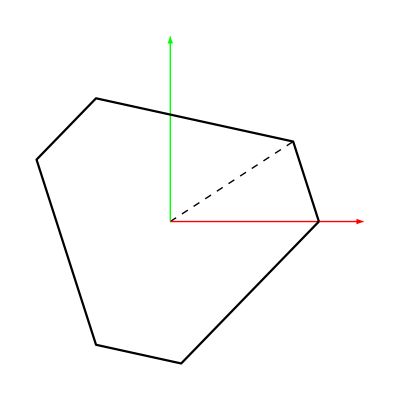

```mathematica
Show[Graphics[{Dashed, Line[{{0,0}, (b/.datap)[[2]][[1;;2]]}]}], Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black], AspectRatio->1, ImageResolution->600]
```

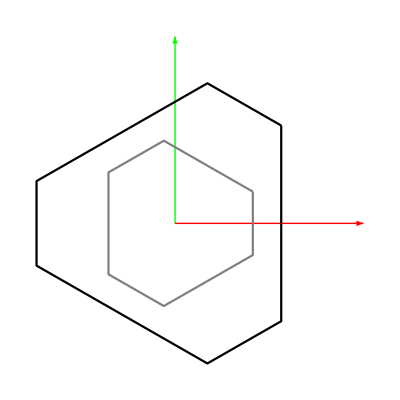

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
(*Locations of all the known ground joints*)
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;

tempb = Table[Symbol["b"<>ToString[i]],{i, 6}];

b = Table[rotZ[(2π/3-2*γb)/2].tempb[[i]],{i, Length[tempb]}];

al1 = {rt, 0, 0};
al2 = rotZ[2*γt].al1;
al3 = rotZ[2π/3].al1;
al4 = rotZ[2π/3].al2;
al5 = rotZ[4π/3].al1;
al6 = rotZ[4π/3].al2;
tempal = Table[Symbol["al"<>ToString[i]],{i, 6}];
al = Table[rotZ[(2π/3-2γt)/2].tempal[[i]],{i, Length[tempal]}];
Show[Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black],ListLinePlot[Join[(al/.datap), {(al/.datap)[[1]]}][[;;, 1;;2]],PlotStyle->Gray], AspectRatio->1, ImageResolution->600]
```

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
l= Table[Symbol["l"<>ToString[i]],{i, 6}];
(*a = Table[Symbol["a"<>ToString[i]],{i, 6}];*)
ϕ = Table[Symbol["ϕ"<>ToString[i]],{i,6}];
ψ = Table[Symbol["ψ"<>ToString[i]],{i,6}];
```

```mathematica
(*Considering ϕi, ψi and li's as the configuration space q*)
(*Rotation matrix of any leg li*)
Rl = Table[rotY[ϕ[[i]]].rotX[ψ[[i]]],{i, 6}];
(*Angular velocity Jacobian of each leg*)
Jωl = Table[SkewMat2vec[Simplify[T[Rl[[i]]].D[Rl[[i]],{Join[ϕ,ψ, l]}]]],{i, 6}];
(*a in global frame via b*)
a  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]},{i, 6}];
```

```mathematica
(*The mid point of the top platform will be*)
ptp = Total[a]/6;
```

```mathematica
(*Now consider the three points a1, a5, a6 so that the local orientation of the top platform is along the global frame*)
a65 = Simplify[((a[[6]]-a[[5]])/Sqrt[((b[[6]]-b[[5]]).(b[[6]]-b[[5]]))/.rb->rt/.γb->γt])];
a15 = Simplify[((a[[1]]-a[[5]])/Sqrt[((b[[1]]-b[[5]]).(b[[1]]-b[[5]]))/.rb->rt/.γb->γt])];
(*a12 and a13 are unit vectors, but the cross need not be a unit vector and hence the Rotation matrix columns need to be re-normalised*)
(*We need to find the magnitude of the second and the third axes*)
```

```mathematica
(*(*Now consider the three points a1, a5, a6 so that the local orientation of the top platform is along the global frame*)
a56 = Simplify[((a[[5]]-a[[6]])/Sqrt[((b[[5]]-b[[6]]).(b[[5]]-b[[6]]))/.rb->rt/.γb->γt])];
a16 = Simplify[((a[[1]]-a[[6]])/Sqrt[((b[[1]]-b[[6]]).(b[[1]]-b[[6]]))/.rb->rt/.γb->γt])];
*)
```

```mathematica
(*sinangle = Simplify[(Cross[(b[[6]]-b[[5]])/Sqrt[(b[[6]]-b[[5]]).(b[[6]]-b[[5]])], (b[[1]]-b[[5]])/Sqrt[(b[[1]]-b[[5]]).(b[[1]]-b[[5]])]]/.rb->rt/.γb->γt)[[3]]];
zaxis = Simplify[Cross[a65, a15]/sinangle];
Rtp = {a65,  Cross[zaxis, a65], zaxis};*)
```

```mathematica
sinangle = Simplify[(Cross[(b[[1]]-b[[6]])/Sqrt[(b[[1]]-b[[6]]).(b[[1]]-b[[6]])], (b[[5]]-b[[6]])/Sqrt[(b[[5]]-b[[6]]).(b[[5]]-b[[6]])]]/.rb->rt/.γb->γt)[[3]]];
zaxis = Simplify[Cross[a16, a56]/sinangle];
Rtp = { Cross[a16, zaxis],a16, zaxis};
```

```mathematica
(*Now that we have obtained the rotation matrix, we can find the angular velocity Jacobian of the top plate*)
Jωt = SkewMat2vec[T[Rtp].D[Rtp,{Join[ϕ, ψ, l]}]];
```

```mathematica
(*CoM of the two parts of the prismatic joints*)
pa  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]-la/2},{i, 6}];
pb  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, lb/2},{i, 6}];
(*First case where ϕi, ψi and li's are given. Contains all the Jacobians*)
Jpai = D[pa, {Join[ϕ, ψ, l]}];
Jpbi = D[pb, {Join[ϕ, ψ, l]}];
Jtp = D[ptp,  {Join[ϕ, ψ, l]}];
```

```mathematica
(*To generate the test data for this system*)
tpdat = {c1->0, c2->0, c3->0, x->0, y->0, z->1.1};
```

```mathematica
qrule =Flatten[Table[{ϕ[[i]]-> ϕ[[i]][t], ψ[[i]]->ψ[[i]][t], l[[i]]->l[[i]][t]},{i, 6}]];
q = Join[ϕ, ψ, l]/.qrule;
```

```mathematica
Amat = vec2SkewMat[{c1, c2, c3}];
Rdat = Simplify[Inverse[(IdentityMatrix[3]-Amat)].(IdentityMatrix[3]+Amat)];
Simplify[Rdat.T[Rdat]]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Rtps = Rtp/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.tpdat;
aldat = al/.datap;
ag =Simplify[Table[{x, y, z}+Rdat.aldat[[i]],{i, 6}]]/.tpdat;
bdat = b/.datap;
```

```mathematica
(*Equating both the points*)
```

```mathematica
eq1 = (ag - bdat);
```

```mathematica
lsample = Inner[Rule, l/.qrule, Table[√(eq1[[i]].eq1[[i]]), {i, 6}], List]
```

{l1[t]→1.20833,l2[t]→1.20833,l3[t]→1.20833,l4[t]→1.20833,l5[t]→1.20833,l6[t]→1.20833}

```mathematica
eq2 = ag - a/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.lsample;
```

```mathematica
(*Considering one of the solutions for Cos in this case taking the first one. This gives the solutions for all the ψ's*)
```

```mathematica
ψt = ψ/.qrule;
ϕt = ϕ/.qrule;
```

```mathematica
ψsample = Flatten[Table[(ψt[[i]]-> ArcTan[Cos[ψt[[i]]], Sin[ψt[[i]]]]/.{Cos[ψt[[i]]]-> √(1-Sin[ψt[[i]]]^2)}/.Solve[eq2[[i]][[2]]==0, Sin[ψt[[i]]]]),{i, 6}]]
```

{ψ1[t]→0.390648,ψ2[t]→0.337095,ψ3[t]→-0.0500618,ψ4[t]→0.0500618,ψ5[t]→-0.337095,ψ6[t]→-0.390648}

```mathematica
ϕsample = Table[ϕt[[i]]-> ArcTan[Cos[ϕt[[i]]], Sin[ϕt[[i]]]]/.Flatten[{Solve[((eq2/.ψsample)[[i]][[1]])==0, Sin[ϕt[[i]]]], Solve[((eq2/.ψsample)[[i]][[3]])==0, Cos[ϕt[[i]]]]}],{i, 6}]
```

{ϕ1[t]→-0.17618,ϕ2[t]→-0.266725,ϕ3[t]→0.423902,ϕ4[t]→0.423902,ϕ5[t]→-0.266725,ϕ6[t]→-0.17618}

```mathematica
sampledat = Join[ϕsample, ψsample, lsample]
```

{ϕ1[t]→-0.17618,ϕ2[t]→-0.266725,ϕ3[t]→0.423902,ϕ4[t]→0.423902,ϕ5[t]→-0.266725,ϕ6[t]→-0.17618,ψ1[t]→0.390648,ψ2[t]→0.337095,ψ3[t]→-0.0500618,ψ4[t]→0.0500618,ψ5[t]→-0.337095,ψ6[t]→-0.390648,l1[t]→1.20833,l2[t]→1.20833,l3[t]→1.20833,l4[t]→1.20833,l5[t]→1.20833,l6[t]→1.20833}

```mathematica
(*Formulating the constraint equations*)
```

```mathematica
η = Join[Simplify[Expand[Table[(a[[i]]-a[[i+1]]).(a[[i]]-a[[i+1]])-(al[[i]]-al[[i+1]]).(al[[i]]-al[[i+1]]),{i, 5}]]], {Simplify[Expand[(a[[6]]-a[[1]]).(a[[6]]-a[[1]])-(al[[6]]-al[[1]]).(al[[6]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[3]]).(a[[1]]-a[[3]])-(al[[3]]-al[[1]]).(al[[3]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[4]]).(a[[1]]-a[[4]])-(al[[1]]-al[[4]]).(al[[1]]-al[[4]])]], Simplify[Expand[(a[[1]]-a[[5]]).(a[[1]]-a[[5]])-(al[[1]]-al[[5]]).(al[[1]]-al[[5]])]], Expand[(a[[1]]-a[[3]]).Cross[a[[1]]-a[[2]], a[[1]]-a[[4]]]], Expand[(a[[1]]-a[[4]]).Cross[a[[1]]-a[[3]], a[[1]]-a[[5]]]], Expand[(a[[1]]-a[[5]]).Cross[a[[1]]-a[[4]], a[[1]]-a[[6]]]]}];
η//Dimensions
(*Variables[η]*)
```

{12}

```mathematica
ηeqn = η/.qrule/.datap/.leglparam/.legmparam/.tpmparam;
(*Variables[ηeqn]*)
```

```mathematica
(*Therefore the sample solution satisfies the constraint equations*)
```

```mathematica
η/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.sampledat
```

{6.10623×10^-16,8.88178×10^-16,7.21645×10^-16,1.77636×10^-15,-2.22045×10^-16,0.,8.88178×10^-16,4.44089×10^-16,4.44089×10^-16,-1.59595×10^-16,-7.91034×10^-16,-3.46945×10^-16}

```mathematica
(*Obtaining an initial condition on velocities*)
```

```mathematica
Jηθ = D[ηeqn,{q[[13;;18]]}];
Jηϕ = D[ηeqn, {q[[1;;12]]}];
```

```mathematica
dϕsample = (-Inverse[Jηϕ/.sampledat].(Jηθ/.sampledat)).{0.1, 0,0,0,0,0}
```

{0.0662406,0.0830384,0.0703517,0.00891622,-0.00377044,0.0302592,0.108352,0.0863335,0.0502908,0.0502908,0.0863335,0.142433}

```mathematica
initvel = Inner[Rule, D[q, t], Join[dϕsample, {0.1, 0,0,0,0,0}], List]
```

{ϕ1'[t]→0.0662406,ϕ2'[t]→0.0830384,ϕ3'[t]→0.0703517,ϕ4'[t]→0.00891622,ϕ5'[t]→-0.00377044,ϕ6'[t]→0.0302592,ψ1'[t]→0.108352,ψ2'[t]→0.0863335,ψ3'[t]→0.0502908,ψ4'[t]→0.0502908,ψ5'[t]→0.0863335,ψ6'[t]→0.142433,l1'[t]→0.1,l2'[t]→0,l3'[t]→0,l4'[t]→0,l5'[t]→0,l6'[t]→0}

```mathematica
tempM = Append[(Table[T[Jpai[[i]]].Jpai[[i]]*ma+T[Jpbi[[i]]].Jpbi[[i]]*mb+T[Jωl[[i]]].Ibi.Jωl[[i]]+T[Jωl[[i]]].Iai.Jωl[[i]],{i, 6}]),T[Jtp].Jtp*mtp+T[Jωt].Itp.Jωt];
tempM//dim
```

{7,18,18}

```mathematica
tempM2 = Total[tempM, {1}];
```

```mathematica
(*Checking the symmetry of the mass matrix*)
```

```mathematica
tempM2 - T[tempM2]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
(*Computing the Cmat from this Mmat*)
```

```mathematica
(*The architecture parameters of the manipulator are substituted here*)
```

```mathematica
tic[]
Mmat = tempM2/.qrule/.datap/.leglparam/.legmparam/.tpmparam;
toc[]
```

Actual time consumed: 7.4229439 seconds.

CPU time consumed: 7.375 seconds.

```mathematica
qvar = Join[ϕ, ψ, l];
dϕ = Table[Symbol["dϕ"<>ToString[i]],{i, 6}];
dψ = Table[Symbol["dψ"<>ToString[i]],{i, 6}];
dl = Table[Symbol["dl"<>ToString[i]],{i, 6}];
dq = Join[dϕ, dψ,dl];
dqrule = Inner[Rule, D[q, t], dq, List];
rqrule= Join[Inner[Rule,q, qvar, List], dqrule];
```

```mathematica
size[Mmat]
```

Size of the expression is:21498.1 KB.

```mathematica
tic[]
n = Length[q];
tempC = Table[0, {ii, 1,n}, {jj, 1,n}];
For [ii = 1, ii ≤ n, 
For[jj = 1, jj ≤ n,
For[kk = 1, kk≤ n, 
tempC[[ii,jj]] +=1/2*( D[Mmat[[ii,jj]], q[[kk]]] + D[Mmat[[ii,kk]], q[[jj]]] - D[Mmat[[jj, kk]], q[[ii]]])*D[q[[kk]],t] ;
kk++];
jj++];
ii++];
toc[]
```

Actual time consumed: 4.719915 seconds.

CPU time consumed: 4.703 seconds.

```mathematica
(*Size of the Cmatrix without simplifying is around 2.45GB*)
size[tempC]
```

Size of the expression is:1.20615×10^6 KB.

```mathematica
(*Since we find Cmat from Mat variables still should be the same, but with their derivatives included*)
```

```mathematica
(*Verifying the property of Cmat*)
```

```mathematica
tic[]
Cdat=tempC/.sampledat/.initvel;
toc[]
```

Actual time consumed: 30.61427 seconds.

CPU time consumed: 30.093 seconds.

```mathematica
(*size[Cdat]*)
```

```mathematica
Mmatdat = D[Mmat, t]/.sampledat/.initvel;
```

```mathematica
tempA = Mmatdat-2*Cdat;
temppA = tempA+T[tempA];
temppA//dim
Chop[Simplify[temppA]]
```

{18,18}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
(*This verifies the nature of the C and M matrices*)
```

```mathematica
(*Formulating the potential term*)
```

```mathematica
tempV = Table[{ma*g*pa[[i]][[3]], mb*g*pb[[i]][[3]]},{i, 6}];
V = Total[Append[Flatten[tempV], mtp*g*ptp[[3]]]]/.qrule/.datap/.leglparam/.legmparam/.tpmparam;
G = D[V, {q}];
```

```mathematica
(*Since the formulation is not done in the generalised coordinates, we need to add the constraint Lagrangian term*)
```

```mathematica
Jηq = D[ηeqn,{q}];
Dimensions[Jηq]
```

{12,18}

```mathematica
dJηq = D[Jηq, t];
```

```mathematica
(*Proceeding to dynamics using Numeric*)
```

```mathematica
(*Using compiled functions to formulate the dynamics*)
```

```mathematica
tMmat = Mmat/.rqrule;
tic[]
cMmat = Compile[{{ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[tMmat]];
toc[]
```

Actual time consumed: 0.184933 seconds.

CPU time consumed: 0.187 seconds.

```mathematica
tCmat = tempC/.rqrule;
tic[]
cCmat = Compile[{{ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}, {dϕ1, _Real},{dϕ2, _Real},{dϕ3, _Real},{dϕ4, _Real},{dϕ5, _Real},{dϕ6, _Real},{dψ1, _Real},{dψ2, _Real},{dψ3, _Real},{dψ4, _Real},{dψ5, _Real},{dψ6, _Real},{dl1, _Real},{dl2, _Real},{dl3, _Real},{dl4, _Real},{dl5, _Real},{dl6, _Real}}, Evaluate[tCmat]];
toc[]
```

Actual time consumed: 9.2272828 seconds.

CPU time consumed: 9.031 seconds.

```mathematica
tGmat = G/.rqrule;
tic[]
cGmat = Compile[{{ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[tGmat]];
toc[]
```

Actual time consumed: 0.01562 seconds.

CPU time consumed: 0. seconds.

```mathematica
tJηq = Jηq/.rqrule;
tic[]
cJηq = Compile[{{ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[tJηq]];
toc[]
```

Actual time consumed: 0.015627 seconds.

CPU time consumed: 0.016 seconds.

```mathematica
tJηϕ = Jηϕ/.rqrule;
tic[]
cJηϕ = Compile[{{ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[tJηϕ]];
toc[]
```

Actual time consumed: 0.015625 seconds.

CPU time consumed: 0.015 seconds.

```mathematica
tJηθ = Jηθ/.rqrule;
tic[]
cJηθ = Compile[{{ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[tJηθ]];
toc[]
```

Actual time consumed: 0.006509 seconds.

CPU time consumed: 0. seconds.

```mathematica
tdJηq = dJηq/.rqrule;
tic[]
cdJηq = Compile[{{ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}, {dϕ1, _Real},{dϕ2, _Real},{dϕ3, _Real},{dϕ4, _Real},{dϕ5, _Real},{dϕ6, _Real},{dψ1, _Real},{dψ2, _Real},{dψ3, _Real},{dψ4, _Real},{dψ5, _Real},{dψ6, _Real},{dl1, _Real},{dl2, _Real},{dl3, _Real},{dl4, _Real},{dl5, _Real},{dl6, _Real}}, Evaluate[tdJηq]];
toc[]
```

Actual time consumed: 0.06903 seconds.

CPU time consumed: 0.063 seconds.

```mathematica
(*Now formulating the RHS terms*)
qcVector[q_?(VectorQ[#,NumericQ]&),dq_?(VectorQ[#,NumericQ]&)]:=Module[{Mval, Cval, Gval, Jηqval, Minv, subs, dJηqval, λ, Qc},

Mval=cMmat@@q;
Cval=cCmat@@Join[q, dq];
Gval=cGmat@@q;

Jηqval=cJηq@@q;
dJηqval = cdJηq@@Join[q, dq];
Minv=Inverse[Mval];

λ=-N[Inverse[(Jηqval.Minv.T[Jηqval])].(dJηqval.dq+Jηqval.Minv.(-Cval.dq-Gval))];
Qc=T[Jηqval].λ;
Return[N[Qc]];
];
```

```mathematica
qcVector[q/.sampledat, D[q, t]/.initvel]
```

{2.54346,3.85991,-6.33208,-6.33831,3.93184,2.34585,-5.51154,-4.91516,0.7262,-0.717796,4.91883,5.54592,-2.3665,-2.39022,-2.38643,-2.4308,-2.41838,-2.253}

```mathematica
(*Formulating the double dots*)
doubledots[q_?(VectorQ[#,NumericQ]&),dq_?(VectorQ[#,NumericQ]&)]:=Module[{Mval, Cval, Gval, LHS},
Mval=cMmat@@q;
Cval=cCmat@@Join[q,dq];
Gval=cGmat@@q;
LHS=-(Inverse[Mval]).(Cval.dq+Gval-qcVector[q,dq]);
Return[LHS];
];
```

```mathematica
doubledots[q/.sampledat, D[q, t]/.initvel]
```

{-1.58829,-2.31381,3.42842,3.42746,-2.32074,-1.58766,3.09758,2.65472,-0.374468,0.376544,-2.6569,-3.12026,-9.12712,-9.12529,-9.12777,-9.13391,-9.1314,-9.11822}

```mathematica
initvel
```

{ϕ1'[t]→0.0662406,ϕ2'[t]→0.0830384,ϕ3'[t]→0.0703517,ϕ4'[t]→0.00891622,ϕ5'[t]→-0.00377044,ϕ6'[t]→0.0302592,ψ1'[t]→0.108352,ψ2'[t]→0.0863335,ψ3'[t]→0.0502908,ψ4'[t]→0.0502908,ψ5'[t]→0.0863335,ψ6'[t]→0.142433,l1'[t]→0.1,l2'[t]→0,l3'[t]→0,l4'[t]→0,l5'[t]→0,l6'[t]→0}

```mathematica
initvel2 = ConstantArray[0, {18}];
```

```mathematica
tic[]
dynsim = NDSolve[{doubledots[q1[t],q1'[t]]==q1''[t],q1[0]==(q/.sampledat),q1'[0]==initvel2},q1,{t,0,1}][[1]]
toc[]
```

{q1→InterpolatingFunction[…]}

Actual time consumed: 1.473143 seconds.

CPU time consumed: 0.5 seconds.

```mathematica
(*Now performing the energy checks needed*)
qsol = (q1/.dynsim);
qsample = Table[qsol[i],{i, 0, 1, 0.01}];
qsample//Dimensions
```

{101,18}

```mathematica
(*Default image size is 800*)
Texplot[xaxis_, yaxis_, imgsize_, xlabel_, ylabel_]:=Module[{magni1, fontsize, markersize, color, markers, flist, f1nonsing},
magni1=2; (*Magnification in axis and axis labesl*)
fontsize=20; (*Axis font label size*)
markersize=20; 
color={Directive[RGBColor[0,0,1]],Directive[Orange],Directive[Red],Directive[Brown],Directive[RGBColor[0.5,0.5,0]],Directive[RGBColor[0,0.6,0]]};
markers={{"+",markersize},{"○",markersize},{"△",markersize},{"□",markersize},{"♢",markersize},{"*",markersize}};

flist=Table[{xaxis[[i]],yaxis[[i]]},{i,1,Length[xaxis],1}];

f1nonsing=ListPlot[{flist},PlotRange->All,BaseStyle->{FontFamily->"Latin Modern Roman"},Frame->True,FrameStyle->{Directive[Black,fontsize],Directive[Black,fontsize]},GridLines->Automatic,PlotStyle->color,PlotMarkers->markers[[1]],FrameLabel->{MaTeX[ToString["\\text{"<>xlabel<>"}"],Magnification->magni1],MaTeX[ToString[ylabel],Magnification->magni1]},Joined->True, ImageSize->imgsize];

Return[f1nonsing];
]
```

```mathematica
time = Table[i, {i, 0, 1, 0.01}];
```

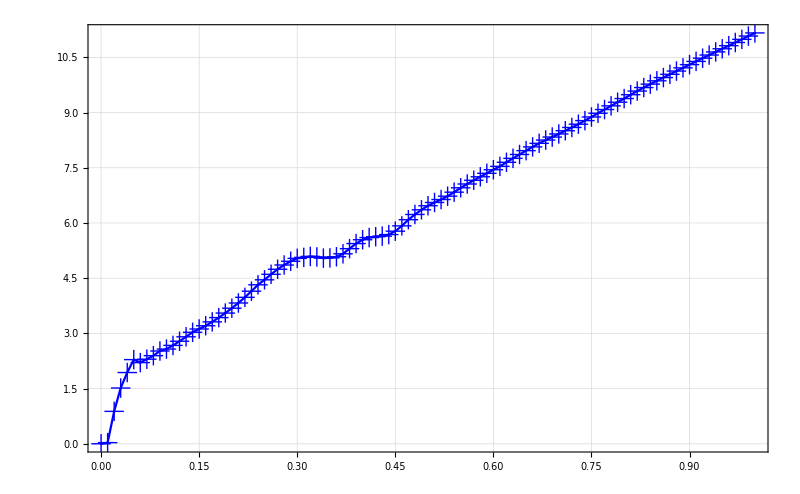

```mathematica
ηtest = Table[Max[Abs[ηeqn/.Inner[Rule,Join[q, D[q, t]], Join[qsol[i], qsol'[i]], List]]],{i, 0,1, 0.01}];
Texplot[time, ηtest*10^7, 800, "Time~(s)", "e_1 (\\times 10^{-7})"]
```

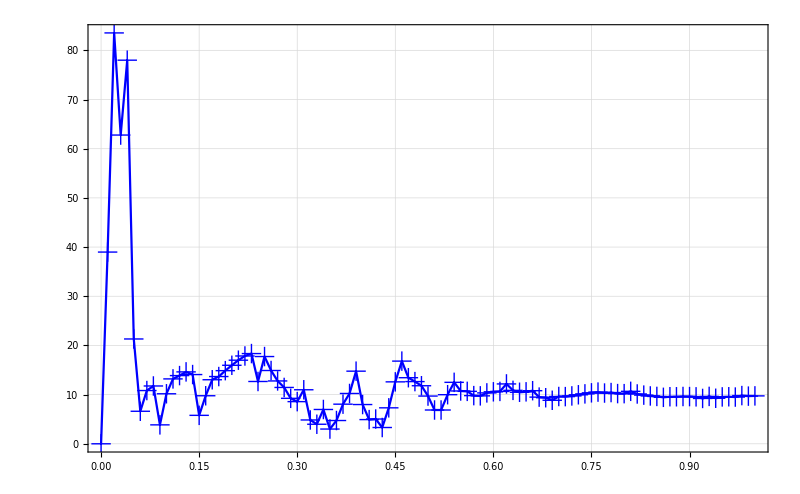

```mathematica
(*2. First order check: Checking the norm of Jηq.q' check*)
Jηqtest = Table[Max[Abs[(cJηq@@qsol[i]).qsol'[i]]],{i, 0, 1, 0.01}];
Texplot[time, Jηqtest*10^7, 800, "Time~(s)", "e_2 (\\times 10^{-7})"]
```

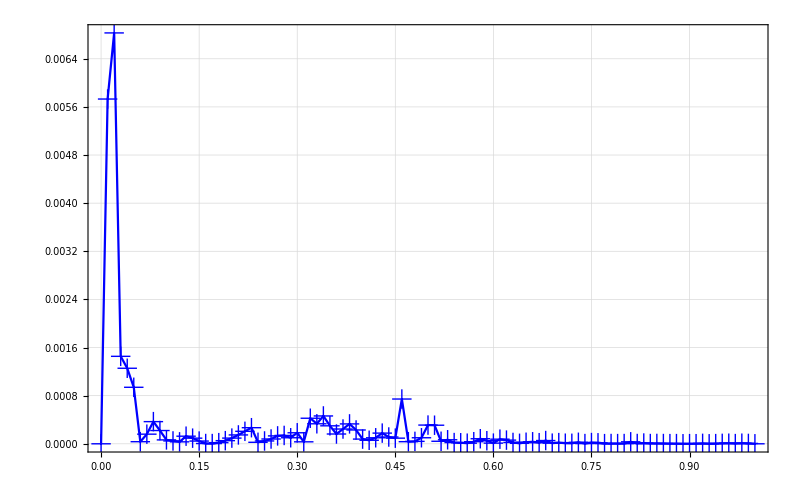

```mathematica
(*3. Second order check: Cheking norm of Jηq.d2q+dJηq.dq*)
dJηqtest = Table[Max[Abs[(cJηq@@qsol[i]).qsol''[i]+(cdJηq@@Join[qsol[i],qsol'[i]]).qsol'[i]]],{i, 0,1 , 0.01}];
Texplot[time, dJηqtest, 800, "Time~(s)", "e_3"]
```

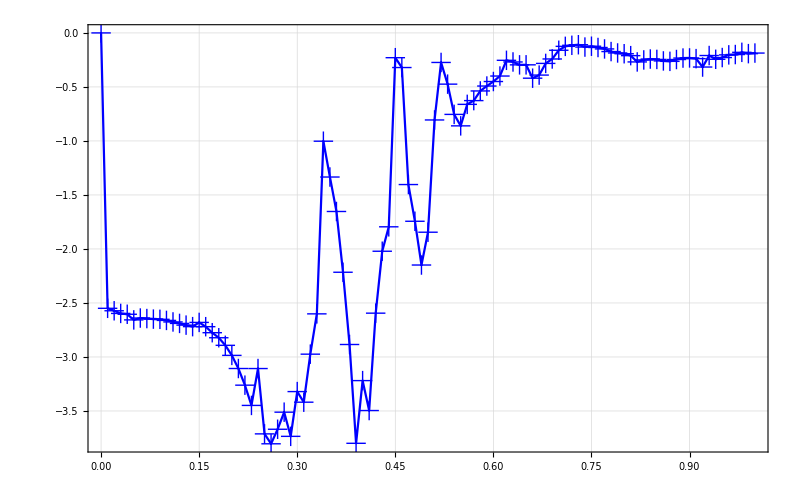

```mathematica
(*4. Energy: Checking Energy constant criteria*)
H = Table[(1/2)*qsol'[i].(cMmat@@qsol[i]).qsol'[i]+(V/.Inner[Rule,Join[q, D[q, t]], Join[qsol[i], qsol'[i]], List]),{i, 0,1, 0.01}];
H1 = ConstantArray[H[[1]], Dimensions[H]];
Texplot[time, (H-H1)/H1*10^7, 800, "Time~(s)", "en (\\times 10^{-7})"]
```

```mathematica
(*We need the extended configuration space values to plot the manipulator. So root-tracking for it*)
Arp = vec2SkewMat[{c1, c2, c3}];
Rtp2 = Simplify[Inverse[(IdentityMatrix[3]-Arp)].(IdentityMatrix[3]+Arp)];
pc = {x, y, z};
aj  = Table[b[[i]]+Rl[[i]].{0,0, l[[i]]},{i, Length[b]}];
atp = Table[pc+Rtp2.al[[i]],{i, Length[al]}];
(*Formulating the simple constraint equations (not the rigidity of the top platform constraint)*)
ηrt = Flatten[(aj-atp)]/.datap/.leglparam/.legmparam/.tpmparam;
```

```mathematica
cη = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[ηrt], RuntimeAttributes->{Listable}, Parallelization->True];
qx = {x, y, z, c1, c2, c3};
tempJn = D[ηrt, {Join[qx, ϕ, ψ]}];
cJn = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real},{ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[tempJn], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
TrackRoot[thetai_, phii_] :=  Module[{nvec, Jmat, δphi, loopcounter, tempphi},
nvec = cη@@Join[phii, thetai];
loopcounter=0;
tempphi = phii;
While[Max[Abs[nvec]]≥ 10^-10,
If[loopcounter≥ 100, Break];
loopcounter++;
Jmat =  cJn@@Join[tempphi, thetai];
δphi=LinearSolve[Jmat,nvec];
tempphi =tempphi-δphi;
nvec = cη@@Join[tempphi, thetai];
];
Return[tempphi];
]
```

```mathematica
linit = l/.(lsample/.rqrule);
ϕinit = Join[{0,0,1.1,0.1,0.1,0}, ϕ/.(ϕsample/.rqrule), ψ/.(ψsample/.rqrule)];
ϕinit - TrackRoot[linit, ϕinit];
qfull = Join[qx, q/.rqrule];
```

```mathematica
(*Tracking the passive and task space variables*)
tempinit = ϕinit;
trackeddat = Table[tempinit = TrackRoot[qsample[[i]][[13;;18]], tempinit];
Join[TrackRoot[qsample[[i]][[13;;18]], tempinit], qsample[[i]][[13;;18]]],{i, Length[qsample]}];
```

```mathematica
qvals = Table[Inner[Rule, qfull, trackeddat[[i]], List], {i, Length[trackeddat]}];
```

```mathematica
plotsrspm[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.3, 1.3}, {-1.3, 1.3}, {-1.3, 1.3}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
(*llinks = Table[Graphics3D[{Purple,Opacity[0.5],Cylinder[{bval[[i]],aval[[i]]/.qvals}, 0.04]}],{i, Length[bval]}];*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.5],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, Length[bval]}];
lainks = Table[Graphics3D[{LightOrange,Opacity[0.5],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
(*Plotting the configuration*)
Show[base, top, jointstop, jointsbase, lainks, lbinks]]
```

```mathematica
mansrspm = Manipulate[
plotsrspm[qvals[[j]]],
{j, 1, Length[qvals], 1}, ContentSize->{400,400}]
```

```mathematica
(*Configuration space dynamics corrected*)
```

```mathematica
(*frames = Table[Export["config"<>ToString[j]<>".jpeg", plotsrspm[qvals[[j]]]],{j, 1, 83, 1}];*)
```

```mathematica
Chop[Rtp/.datap/.qvals[[1]]]
```

{{1.,0,0},{0,1.,0},{0,0,1.}}

```mathematica
Chop[Rtp/.datap/.qvals[[-1]]]
```

{{0.999994,0,-0.00331968},{0,1.,0},{0.00331968,0,0.999994}}

```mathematica
(*Export these matrices to simulate the system in C++*)
```

```mathematica
(*Writing a general function to take any Mathematica expression into a C compatible file or into a template file*)
```

```mathematica
trigrep[i_]:={Cos[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ToExpression[Symbol[ToString[lambda]<>ToString[i]]],Sin[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ToExpression[Symbol[ToString[mu]<>ToString[i]]],Sec[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> 1/(ToExpression[Symbol[ToString[lambda]<>ToString[i]]]),Csc[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> 1/(ToExpression[Symbol[ToString[mu]<>ToString[i]]]),Tan[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ((ToExpression[Symbol[ToString[mu]<>ToString[i]]])/(ToExpression[Symbol[ToString[lambda]<>ToString[i]]])),Cot[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ((ToExpression[Symbol[ToString[lambda]<>ToString[i]]])/(ToExpression[Symbol[ToString[mu]<>ToString[i]]]))};
alpharep[i_]:={ToExpression[Symbol[ToString[α]<>ToString[i]]]-> ToExpression[Symbol[ToString[alpha]<>ToString[i]]]};
alpharepall=Union[alpharep[1],alpharep[2],alpharep[3],alpharep[4],alpharep[5],alpharep[6]];
revtrigrep[i_]:=Reverse[trigrep[i],2];
trigrepall=Union[trigrep[1],trigrep[2],trigrep[3],trigrep[4],trigrep[5],trigrep[6]];
revtrigrepall=Union[revtrigrep[1],revtrigrep[2],revtrigrep[3],revtrigrep[4],revtrigrep[5],revtrigrep[6]];
revreplist=Reverse[replist,2];
revalpharepall=Reverse[alpharepall,2];
inversetrig =  Union[{ArcTan[x_, y_]->atan2[y,x]} , {ArcCos[x_]->acos[x]}];
replist=Union[{Power-> pow},trigrepall,{Sin[x_]-> sin[x]},{Cos[x_]-> cos[x]},{Tan[x_]-> tan[x]},{Csc[x_]-> 1/sin[x]},{Sec[x_]-> 1/cos[x]},{Cot[x_]->sin[x]/cos[x]}];
Print["Change the angles from Greek symbols"]
```

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[replist,2].

Change the angles from Greek symbols

```mathematica
phi = Table[Symbol["p"<>ToString[i]],{i, 6}];
psi = Table[Symbol["s"<>ToString[i]],{i, 6}];
dphi = Table[Symbol["dp"<>ToString[i]],{i, 6}];
dpsi = Table[Symbol["ds"<>ToString[i]],{i, 6}];
nogreek = Join[Inner[Rule, ϕ, phi, List], Inner[Rule, ψ, psi, List], Inner[Rule, dϕ, dphi, List], Inner[Rule, dψ, dpsi, List]];
```

```mathematica
cospsi = Table[Symbol["cs"<>ToString[i]],{i, 6}];
sinpsi = Table[Symbol["ss"<>ToString[i]],{i, 6}];
cosphi = Table[Symbol["cp"<>ToString[i]],{i, 6}];
sinphi = Table[Symbol["sp"<>ToString[i]],{i, 6}];
```

```mathematica
trigtoalg = Join[Inner[Rule, Cos[ψ], cospsi, List], Inner[Rule, Sin[ψ], sinpsi, List], Inner[Rule, Cos[ϕ], cosphi, List], Inner[Rule, Sin[ϕ], sinphi, List]];
```

```mathematica
(*Exporting Mmat*)
```

```mathematica
PortMmattoC[tMmat_]:=Module[{tMmat2, diagtMmat, tMmat2alg, diagtMmatalg, tempMtoc1, Mmat1toc, tempMtoc2, Mmat2toc},
tMmat2 = tMmat;
(*Getting the lower triangular matrix*)
For[i=1, i≤ Length[tMmat], i++, 
For[j=i, j≤Length[tMmat], j++, 
tMmat2[[i,j]]=0;
];
];
(*Getting the diagonal matrix*)
diagtMmat = DiagonalMatrix[Diagonal[tMmat]];
(*Converting the trigonometric variables into algebraic variables *)
tMmat2alg = tMmat2/.trigtoalg;
diagtMmatalg = diagtMmat/.trigtoalg;
(*We have the expressions ready to be ported to cpp*)

(*Converting matrices into vectors*)
tempMtoc1 = Flatten[tMmat2alg]/.replist/.inversetrig;
Mmat1toc = StringTake[ToString[Table[CForm[tempMtoc1[[i]]],{i, Length[tempMtoc1]}]],{2,-2}];

tempMtoc2 = Flatten[diagtMmatalg]/.replist/.inversetrig;
Mmat2toc = StringTake[ToString[Table[CForm[tempMtoc2[[i]]],{i, Length[tempMtoc2]}]],{2,-2}];

(*FileTemplateApply[file,<|"Mexpressions1"-> Mmat1toc, "Mexpressions2"-> Mmat2toc|>, "dyn_funcs_test.h"];*)
Return[{Mmat1toc, Mmat2toc}]
]
```

```mathematica
Mmattoc = PortMmattoC[tMmat];
```

```mathematica
(*Trying to extract Cmat similarly*)
```

```mathematica
(*Export any matrix or vector*)
```

```mathematica
PortMattoC[mat_]:=Module[{tempMattoC, mattoC},
(*Substitute all Greek letters and flatten matrices into vectors*)
tempMattoC = Flatten[mat]/.trigtoalg/.replist/.inversetrig/.nogreek;
mattoC  = StringTake[ToString[Table[CForm[tempMattoC[[i]]],{i, Length[tempMattoC]}]],{2,-2}];
Return [mattoC];
]
```

```mathematica
Gmattoc = PortMattoC[tGmat];
Jetaqtoc = PortMattoC[tJηq];
dJetaqtoc = PortMattoC[tdJηq];
```

```mathematica
(*PortMattoC[tGmat, file, "Gexpressions1", "dyn_funcs_test.h"]*)
```

```mathematica
(*PortMattoC[tJηq, file, "Jetaqexpressions1", "dyn_funcs_test.h"]*)
```

```mathematica
(*PortMattoC[tdJηq, file, "dJetaqexpressions1", "dyn_funcs_test.h"]*)
```

```mathematica
file = Import["dyn_funcs.h", "Text"];
```

```mathematica
FileTemplateApply[file,<|"dJetaqexpressions1"->dJetaqtoc, "Jetaqexpressions1"->Jetaqtoc, "Gexpressions1"->Gmattoc, "Mexpressions1"-> Mmattoc[[1]], "Mexpressions2"-> Mmattoc[[2]]|>, "CPP/dyn_funcs_test.h"];
```

```mathematica
(*Exporting sample data to verify ported functions*)
```

```mathematica
(*sampledat2 = sampledat/.rqrule*)
```

```mathematica
(*qval = Flatten[q/.sampledat]*)
```

```mathematica
(*PortMattoC[tJηq/.sampledat2]*)
```

```mathematica
(*initvel1 = initvel/.rqrule*)
```

```mathematica
(*PortMattoC[tdJηq/.sampledat2/.initvel1]*)
```

```mathematica
(*PortMattoC[Cdat]*)
```

```mathematica
(*initvel1*)
```

```mathematica
(*PortMattoC[D[q/.initvel, t]/.initvel]*)
```

```mathematica
(*file2 = Import["cmat_test.h", "Text"];*)
```

```mathematica
(*Dissecting and exporting Cmat*)
```

```mathematica
file = Import["ctemplate.txt", "Text"];
```

```mathematica
PortElementsToC[mat_, elementTemplate_]:=Module[{tempMattoC, mattoC, fname},
(*Substitute all Greek letters and flatten matrices into vectors*)
(*tempMattoC = Flatten[mat]/.trigtoalg/.replist/.inversetrig/.nogreek;
mattoC  = Table[CForm[tempMattoC[[i]]],{i, Length[tempMattoC]}];*)
For[ii=1, ii≤ Length[tCmat],ii++,
For[jj=1, jj≤Length[tCmat],jj++,
tempMattoC = mat[[ii, jj]]/.trigtoalg/.replist/.inversetrig/.nogreek;
mattoC  = CForm[tempMattoC];

fname = ToString["Cmat"<>StringTake["0"<>ToString[ii],-2]<>StringTake["0"<>ToString[jj],-2]];
FileTemplateApply[elementTemplate,<|"fname"->fname , "expression"-> ToString[mattoC]|>, ToString["CPP/Cmat/"<>fname<>".cpp"]];
]
]
]
```

```mathematica
PortElementsToC[tCmat, file];
```

```mathematica
(*(*Verifying the data generated by the cpp codes*)
(*Verifying the C++ data*)

qxdat = Import["qxdata.dat"];
dqxdat = Import["dqxdata.dat"];
dddat = Import["dddata.dat"];*)
```

```mathematica
(*(*1. Zeroth order check: Checking the norm of the loop closure througout the motion*)

ηtest2 = Table[Norm[ηeqn/.Inner[Rule,q, qxdat[[i]][[2;;]],List]],{i,Length[qxdat]}];*)
```

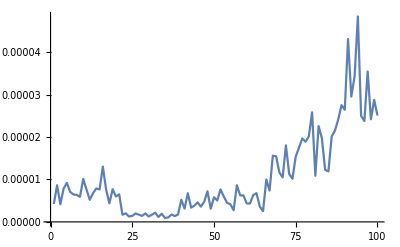

```mathematica
(*ListLinePlot[ηtest2, PlotRange->All]*)
```

```mathematica
(*(*2. First order check: Checking the norm of Jηq.q' check*)

Jηqtest2 = Table[Norm[cJηq@@qxdat[[i]][[2;;]].dqxdat[[i]][[2;;]]],{i,Length[qxdat]}];*)
```

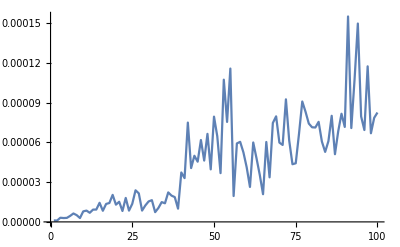

```mathematica
(*ListLinePlot[Jηqtest2, PlotRange->All]*)
```

```mathematica
(*Max[Jηqtest2]*)
```

0.000154859

```mathematica
(*(*Seconds order test*)
dJηqtest = Table[Norm[cJηq@@qxdat[[i]][[2;;]].dddat[[i]][[2;;]]+cdJηq@@Join[qxdat[[i]][[2;;]], dqxdat[[i]][[2;;]]].dqxdat[[i]][[2;;]]],{i,Length[qxdat]}];*)
```

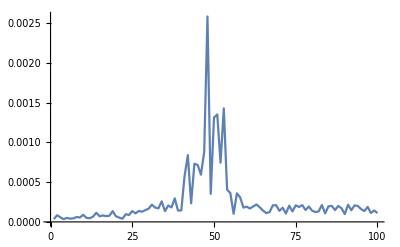

```mathematica
(*ListLinePlot[dJηqtest, PlotRange->All]*)
```

```mathematica
(*(*4. Energy: Checking Energy constant criteria*)
H2 = Table[(1/2)*dqxdat[[i]][[2;;]].cMmat@@qxdat[[i]][[2;;]].dqxdat[[i]][[2;;]]+(V/.Inner[Rule,q, qxdat[[i]][[2;;]], List]),{i,Length[qxdat]}];*)
```

```mathematica
(*H12 = ConstantArray[H2[[1]], Dimensions[H2]];*)
```

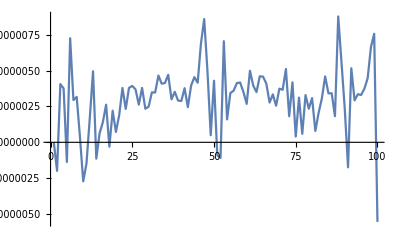

```mathematica
(*ListLinePlot[(H2-H12)/H12, PlotRange->All]*)
```